# Inverse

## Basic Examples

Inverse of a 2x2 matrix:

```mathematica
Inverse[RandomReal[1,{3,3}]]
```

{{-0.256055,1.85301,-0.915877},{0.070775,-1.19225,2.13226},{1.28306,-0.32074,-0.654704}}

Enter the matrix in a grid:

```mathematica
Inverse[({{1, 2, 3}, {4, 5, 6}, {7, 3, 9}})]
```

{{-9/10,3/10,1/10},{-1/5,2/5,-1/5},{23/30,-11/30,1/10}}

Inverse of a symbolic matrix:

```mathematica
Inverse[{{u,v},{v,u}}]
```

{{u/(u^2-v^2),-v/(u^2-v^2)},{-v/(u^2-v^2),u/(u^2-v^2)}}

## Applications

Exact inverse of a Hilbert matrix:

```mathematica
Inverse[HilbertMatrix[5]]//MatrixForm
```

(25 | -300 | 1050 | -1400 | 630
-300 | 4800 | -18900 | 26880 | -12600
1050 | -18900 | 79380 | -117600 | 56700
-1400 | 26880 | -117600 | 179200 | -88200
630 | -12600 | 56700 | -88200 | 44100)

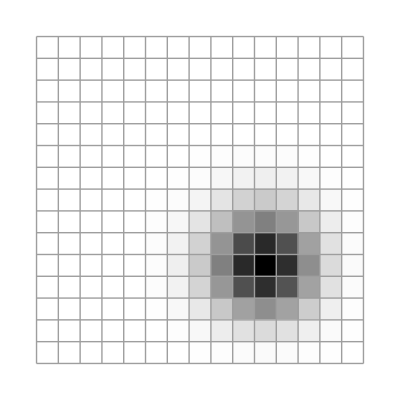

```mathematica
ArrayPlot[Inverse[HilbertMatrix[15]],Mesh->True]
```

Plot the imaginary parts of a Vandermonde matrix for a discrete Fourier transform:

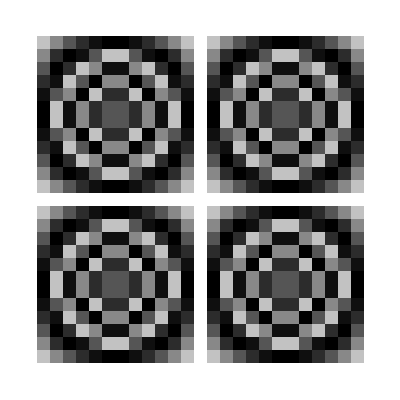

```mathematica
ArrayPlot[Im[Inverse[Table[Exp[2Pi I i j/26.],{i,25},{j,25}]]]]
```

Plot the inverse of a matrix, shading according to absolute value:

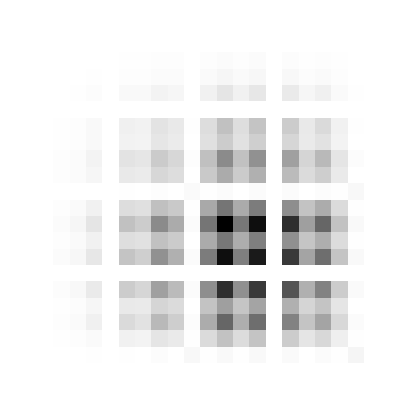

```mathematica
ArrayPlot[Inverse[Table[(1+Mod[i j,10])/(i+j),{i,20},{j,20}]]]
```

Show positive entries as black and others as white:

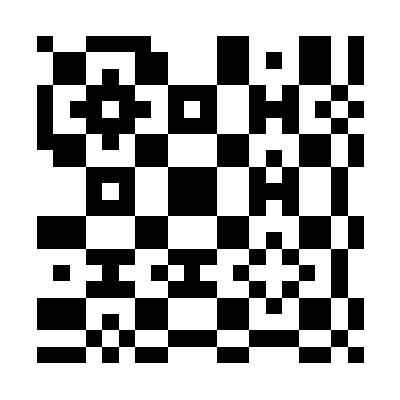

```mathematica
ArrayPlot[Inverse[Table[(1+Mod[i j,10])/(i+j),{i,20},{j,20}]],ColorFunction->(If[#>0,Black,White]&),ColorFunctionScaling->False]
```

## Properties & Relations

```mathematica
m={{a,b},{c,d}};
```

```mathematica
Inverse[m].m
```

{{-(b c)/(-b c+a d)+(a d)/(-b c+a d),0},{0,-(b c)/(-b c+a d)+(a d)/(-b c+a d)}}

```mathematica
Simplify[Inverse[m].m]
```

{{1,0},{0,1}}